# QHD-2 Zero Point Motion in Energy Exchange between Two Oscillators

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Second Order Quantized Hamilton Dynamics (QHD-2) is applied to the energy exchange between two harmonic oscillators coupled by an anharmonic term. QHD-2 gives an approximation to the Heisenberg Equations of Motion (EOM). The QHD commands used in this document are included in QUANTUM, which is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Prezhdo and Pereverzev in J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf
.

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ]
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationships and Hamiltonian J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565

The Hamiltoninan and commutation relationships that are defined below are those used by Prezhdo and Pereverzev in J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf. In order to enter the templates and symbols □_□, □_□^□, ⟦□,□⟧_-, ω, λ and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]su[ESC], [ESC]supo[ESC], [ESC]comm[ESC], [ESC]omega[ESC], [ESC]lambda[ESC] and [ESC]ii[ESC]

```mathematica
SetQuantumObject[q,p];
⟦Subscript[q, 1],Subscript[p, 1]⟧_-=ⅈ;
⟦Subscript[q, 2],Subscript[p, 2]⟧_-=ⅈ;
⟦Subscript[q, 1],Subscript[p, 2]⟧_-=0;
⟦Subscript[q, 2],Subscript[p, 1]⟧_-=0;
⟦Subscript[q, 1],Subscript[q, 2]⟧_-=0;
⟦Subscript[p, 1],Subscript[p, 2]⟧_-=0;
zph=Subscript[p, 1]^2/2+(Subscript[ω, 1]^2*Subscript[q, 1]^2)/2+Subscript[p, 2]^2/2+(Subscript[ω, 2]^2*Subscript[q, 2]^2)/2+λ*Subscript[q, 1]·Subscript[q, 2]^2
```

p_1^2/2+p_2^2/2+1/2 q_1^2 ω_1^2+1/2 q_2^2 ω_2^2+λ q_1·q_2^2

## Heisenberg Equations of Motion and Cross Terms Approximation

The evolution of the expected value of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
The Heisenberg EOM can be calculated using the QHD-Mathematica command QHDEOM, as shown below. The first argument specifies the QHD-order, which is set below to ∞ so that no QHD closure is made in this first example. The second argument is the list of observables. In this example we are intereted in those obsevables needed to calculate the harmonic energies, {p_1^2, p_2^2, q_1^2, q_1^2}. The third argument is the Hamiltonian, remember that it was stored in variable zph above in this document. Finally options can be included, for example QHDHBar→1 specifies that reduced Planck’s constant (Dirac constant) will take the value of 1 (The → symbol can be entered by pressing the keys [ESC]->[ESC], that is [ESC][MINUS][GREATERTHAN][ESC]). The output of QHDEOM can be stored in a variable; it is stored in zeom, then it is shown in a nice format with the command QHDForm below:

```mathematica
zeom=QHDEOM[∞,{Subscript[p, 1]^2,Subscript[p, 2]^2,Subscript[q, 1]^2,Subscript[q, 2]^2},zph,QHDHBar->1];
QHDForm[zeom]
```

No closure was applied
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1^2⟩)/d𝓉=-2 λ ⟨p_1⟩ ⟨q_2^2⟩-2 ω_1^2 ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 ω_2^2 ⟨p_2 q_2⟩_𝓈-4 λ ⟨q_1⟩ ⟨p_2 q_2⟩_𝓈
(d⟨q_1^2⟩)/d𝓉=2 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 ⟨p_2 q_2⟩_𝓈

Notice that the EOM contain new expectation values, for example ⟨p_1·q_1⟩_s=⟨(p_1·q_1+q_1·p_1)/2⟩
The label above the EOM specifies that QHDCrossTermsApproximant was used as an approximation. The definition of this approximation is shown below:

```mathematica
? QHDCrossTermsApproximant
```

QHDCrossTermsApproximant[expr] approximates expected values of crossterms ⟨SubsuperscriptBox["p", "1", "n"]·SubsuperscriptBox["p", "2", "m"]⟩≈⟨SubsuperscriptBox["p", "1", "n"]⟩⟨SubsuperscriptBox["p", "2", "m"]⟩ in expr

We can get the Heisenberg EOM without approximation using QHDApproximantFunction→Identity as the last argument of QHDEOM, as shown below:

```mathematica
zeo2=QHDEOM[∞,{Subscript[p, 1]^2,Subscript[p, 2]^2,Subscript[q, 1]^2,Subscript[q, 2]^2},zph,QHDHBar->1,QHDApproximantFunction->Identity];
QHDForm[zeo2]
```

No closure was applied
(d⟨p_1^2⟩)/d𝓉=-2 ω_1^2 ⟨p_1 q_1⟩_𝓈-2 λ ⟨p_1 q_2^2⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 ω_2^2 ⟨p_2 q_2⟩_𝓈-4 λ ⟨p_2 q_1 q_2⟩_𝓈
(d⟨q_1^2⟩)/d𝓉=2 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 ⟨p_2 q_2⟩_𝓈

Products of operators were symmetrized, for example: ⟨p_2·q_1·q_2⟩_𝓈=1/2⟨p_2·q_1·q_2⟩+1/2⟨q_2·q_1·p_2⟩

## QHD-2 Closure Approximation

Equations of motion (EOM) were obtained above for those variables, {p_1^2, p_2^2, q_1^2, q_1^2}, that are needed for calculation of the harmonic energies. Those calculations are by default performed with cross-term approximations ⟨p_1·p_2⟩≈⟨p_1⟩⟨p_2⟩, and it is possible to recalculate the EOM without approximation using QHDApproximantFunction→Identity. In any case, new expected values like ⟨p_1 q_1⟩_𝓈  are included in those EOM. If the EOM of those new expected values is calculated, more expected values will be generated, building an infinite hierarchy of EOM. Therefore, a closure procedure is applied in order to have a finite hierarchy of EOM. For instance, the approximation:
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
is used to approximate third-order expected values like ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the firts and second order expected values ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. Such a QHD-2 hierarchy is obtained below as the output of the command QHDHierarchy with the first argument set to 2. Same as above, the second argument is the initial list of expected values in the hierarchy, the third argument is the hamiltonian, and optional arguments can be given after that. The output of QHDHierarchy is stored in the variable zphier, and it is shown using the QHDForm command below:

```mathematica
zphier=QHDHierarchy[2,{Subscript[p, 1]^2,Subscript[p, 2]^2,Subscript[q, 1]^2,Subscript[q, 2]^2},zph,QHDHBar->1];
QHDForm[ zphier ]
```

Closure procedure was applied to order 2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1^2⟩)/d𝓉=-2 λ ⟨p_1⟩ ⟨q_2^2⟩-2 ω_1^2 ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2 ω_2^2 ⟨p_2 q_2⟩_𝓈-4 λ ⟨q_1⟩ ⟨p_2 q_2⟩_𝓈
(d⟨q_1^2⟩)/d𝓉=2 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1⟩)/d𝓉=-ω_1^2 ⟨q_1⟩-λ ⟨q_2^2⟩
(d⟨p_1 q_1⟩_𝓈)/d𝓉=⟨p_1^2⟩-ω_1^2 ⟨q_1^2⟩-λ ⟨q_1⟩ ⟨q_2^2⟩
(d⟨q_1⟩)/d𝓉=⟨p_1⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=⟨p_2^2⟩-ω_2^2 ⟨q_2^2⟩-2 λ ⟨q_1⟩ ⟨q_2^2⟩

A EOM hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

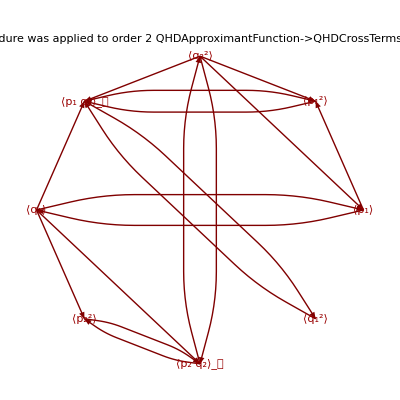

```mathematica
QHDGraphPlot[zphier]
```

The command QHDDifferentialEquations formats the output of QHDHierarchy as standard Mathematica equations, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output zphier that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[zphier]
```

{⟨p_1^2⟩'[𝓉]==-2 λ ⟨p_1⟩[𝓉] ⟨q_2^2⟩[𝓉]-2 ω_1^2 ⟨(p_1·q_1)_𝓈⟩[𝓉],⟨p_2^2⟩'[𝓉]==-2 ω_2^2 ⟨(p_2·q_2)_𝓈⟩[𝓉]-4 λ ⟨q_1⟩[𝓉] ⟨(p_2·q_2)_𝓈⟩[𝓉],⟨q_1^2⟩'[𝓉]==2 ⟨(p_1·q_1)_𝓈⟩[𝓉],⟨q_2^2⟩'[𝓉]==2 ⟨(p_2·q_2)_𝓈⟩[𝓉],⟨p_1⟩'[𝓉]==-ω_1^2 ⟨q_1⟩[𝓉]-λ ⟨q_2^2⟩[𝓉],⟨(p_1·q_1)_𝓈⟩'[𝓉]==⟨p_1^2⟩[𝓉]-ω_1^2 ⟨q_1^2⟩[𝓉]-λ ⟨q_1⟩[𝓉] ⟨q_2^2⟩[𝓉],⟨q_1⟩'[𝓉]==⟨p_1⟩[𝓉],⟨(p_2·q_2)_𝓈⟩'[𝓉]==⟨p_2^2⟩[𝓉]-ω_2^2 ⟨q_2^2⟩[𝓉]-2 λ ⟨q_1⟩[𝓉] ⟨q_2^2⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[zphier,QHDSymbolForTime->z]
```

{⟨p_1^2⟩'[z]==-2 λ ⟨p_1⟩[z] ⟨q_2^2⟩[z]-2 ω_1^2 ⟨(p_1·q_1)_𝓈⟩[z],⟨p_2^2⟩'[z]==-2 ω_2^2 ⟨(p_2·q_2)_𝓈⟩[z]-4 λ ⟨q_1⟩[z] ⟨(p_2·q_2)_𝓈⟩[z],⟨q_1^2⟩'[z]==2 ⟨(p_1·q_1)_𝓈⟩[z],⟨q_2^2⟩'[z]==2 ⟨(p_2·q_2)_𝓈⟩[z],⟨p_1⟩'[z]==-ω_1^2 ⟨q_1⟩[z]-λ ⟨q_2^2⟩[z],⟨(p_1·q_1)_𝓈⟩'[z]==⟨p_1^2⟩[z]-ω_1^2 ⟨q_1^2⟩[z]-λ ⟨q_1⟩[z] ⟨q_2^2⟩[z],⟨q_1⟩'[z]==⟨p_1⟩[z],⟨(p_2·q_2)_𝓈⟩'[z]==⟨p_2^2⟩[z]-ω_2^2 ⟨q_2^2⟩[z]-2 λ ⟨q_1⟩[z] ⟨q_2^2⟩[z]}

## Solution of the QHD-2 Equations: Zero Point Energy

Next we evaluate the hierarchy with the numerical values of the parameters that were used by Prezhdo and Pereverzev in their paper. The result of that evaluation is stored in the variable zpnumhier:

```mathematica
zpnumhier=zphier/.{Subscript[ω, 1]->1.0,Subscript[ω, 2]->1.1,λ-> -0.11};
QHDForm[zpnumhier]
```

Closure procedure was applied to order 2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨p_1^2⟩)/d𝓉=0.22 ⟨p_1⟩ ⟨q_2^2⟩-2. ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=-2.42 ⟨p_2 q_2⟩_𝓈+0.44 ⟨q_1⟩ ⟨p_2 q_2⟩_𝓈
(d⟨q_1^2⟩)/d𝓉=2 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1⟩)/d𝓉=-1. ⟨q_1⟩+0.11 ⟨q_2^2⟩
(d⟨p_1 q_1⟩_𝓈)/d𝓉=⟨p_1^2⟩-1. ⟨q_1^2⟩+0.11 ⟨q_1⟩ ⟨q_2^2⟩
(d⟨q_1⟩)/d𝓉=⟨p_1⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=⟨p_2^2⟩-1.21 ⟨q_2^2⟩+0.22 ⟨q_1⟩ ⟨q_2^2⟩

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[ zpnumhier, 0 ]
```

{⟨p_1^2⟩[0]==■,⟨p_2^2⟩[0]==■,⟨q_1^2⟩[0]==■,⟨q_2^2⟩[0]==■,⟨p_1⟩[0]==■,⟨(p_1·q_1)_𝓈⟩[0]==■,⟨q_1⟩[0]==■,⟨(p_2·q_2)_𝓈⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. These initial conditions are used in  J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf
The initial conditions are stored in the variable zpinicond below:

```mathematica
zpinicond={⟨Subscript[p, 1]^2⟩[0]==0.5,⟨Subscript[p, 2]^2⟩[0]==0.5,⟨Subscript[q, 1]^2⟩[0]==0.5,⟨Subscript[q, 2]^2⟩[0]==0.5,⟨Subscript[p, 1]⟩[0]==0.0,⟨Subscript[(Subscript[p, 1]·Subscript[q, 1]), 𝓈]⟩[0]==0.0,⟨Subscript[q, 1]⟩[0]==0.0,⟨Subscript[(Subscript[p, 2]·Subscript[q, 2]), 𝓈]⟩[0]==0.0}
```

{⟨p_1^2⟩[0]==0.5,⟨p_2^2⟩[0]==0.5,⟨q_1^2⟩[0]==0.5,⟨q_2^2⟩[0]==0.5,⟨p_1⟩[0]==0.,⟨(p_1·q_1)_𝓈⟩[0]==0.,⟨q_1⟩[0]==0.,⟨(p_2·q_2)_𝓈⟩[0]==0.}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable zpnumhier), the initial conditions (which were stored in zpinicond), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) any function of the dynamical variables (expected values), as it will be shown below in this document. The output is stored in the variable zpsol in the calculation below:

```mathematica
zpsol=QHDNDSolve[zpnumhier,zpinicond,0,50]
```

{{⟨p_1^2⟩→InterpolatingFunction[{{0.,50.}},<>],⟨p_2^2⟩→InterpolatingFunction[{{0.,50.}},<>],⟨q_1^2⟩→InterpolatingFunction[{{0.,50.}},<>],⟨q_2^2⟩→InterpolatingFunction[{{0.,50.}},<>],⟨p_1⟩→InterpolatingFunction[{{0.,50.}},<>],⟨(p_1·q_1)_𝓈⟩→InterpolatingFunction[{{0.,50.}},<>],⟨q_1⟩→InterpolatingFunction[{{0.,50.}},<>],⟨(p_2·q_2)_𝓈⟩→InterpolatingFunction[{{0.,50.}},<>]}}

The expression for the harmonic energies of the system are stored in the list energies below:

```mathematica
energies={Subscript[p, 1]^2/2+Subscript[ω, 1]^2 Subscript[q, 1]^2/2,Subscript[p, 2]^2/2+Subscript[ω, 2]^2 Subscript[q, 2]^2/2}/.{Subscript[ω, 1]->1.0,Subscript[ω, 2]->1.1}
```

{p_1^2/2+0.5 q_1^2,p_2^2/2+0.605 q_2^2}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable zpsol. The first argument specifies the expression that we want to plot (graph) as a function of time. The two harmonic energies are shown below:

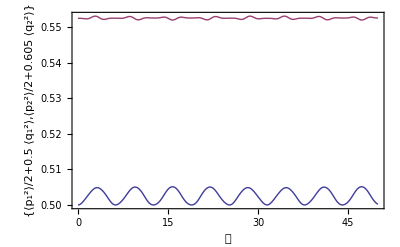

```mathematica
QHDPlot[energies,zpsol]
```

QHDPlot accepts the same options as the standard Mathematica command Plot. Some of those options are used to reproduce part of a graph from Prezhdo and Pereverzev, see below:

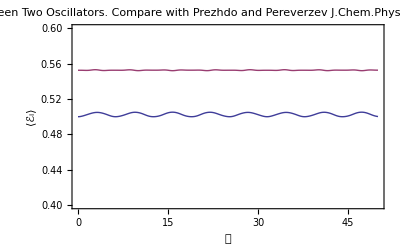

```mathematica
QHDPlot[energies,zpsol,
PlotRange->{0.4,0.6},
FrameLabel->{𝓉,HoldForm[⟨Subscript[ℰ, i]⟩]},
PlotLabel->"Zero Point Motion in Energy Exchange between Two Oscillators.\nCompare with Prezhdo and Pereverzev\nJ.Chem.Phys. Vol 113 No 16, October 2000\nPages 6557-6565 Fig. 5"]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx